

```mathematica
ResourceFunction["DarkMode"][False]
Graph[{1<->2,2<->3,3<->1}]
```

```mathematica
GeoGraphics[GeoBoundsRegion[{{28.0600,28.0900},{-82.4843, -82.4481}}]]
```

-Graphics-

```mathematica
OSMImport=ResourceFunction["OSMImport"]
```

```mathematica
osm=ResourceFunction["OSMImport"][GeoBoundsRegion[{{28.0600,28.0900},{-82.4843, -82.4481}}]]
```

```mathematica
osm2 = ResourceFunction["OSMImport"][GeoBoundsRegion[{{45.0600,45.0900},{-93.2943, -93.2621}}]]
```

XML`Parser`XMLGet::prserr: Invalid character in attribute value (Unicode: 0xv) at Line: 64272 Character: 25 in C:\Users\isaia\AppData\Local\Temp\m-235967de-14bb-4a08-a04c-ad7d7b3e9d35\map.osm.

Import::fmterr: Cannot import data as XML format.

Part::partw: Part 1 of {} does not exist.

<|Nodes→<||>,Ways→<||>|>

```mathematica
Keys[osm]
```

{Nodes,Ways}

```mathematica
Head[osm]
```

Association

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@Select[osm["Ways"],KeyExistsQ[#Tags,"footway"]&]]]
```

-Graphics-

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@Select[osm["Ways"],MatchQ[#[["Tags","highway"]],"sidewalk" | "path" | "footway" | "crosswalk"]&]]]
```

-Graphics-

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@Select[osm["Ways"],MatchQ[#[["Tags","highway"]],"primary" | "secondary" | "tertiary" | "residential"]&]]]
```

-Graphics-

```mathematica
RepeatedTiming[Table[i, {i, 1, 100000000}] // Shallow]
```

{2.13549,{1,2,3,4,5,6,7,8,9,10,«99999990»}}

```mathematica
$RecursionLimit = 1000000
```

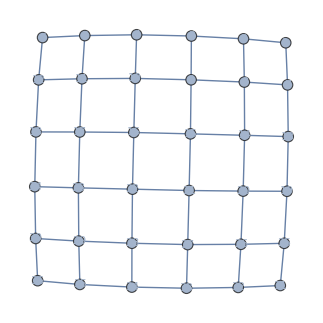

```mathematica
squareGraph[n_Integer]:=
Graph[Flatten[{Table[Table[i*n+j<-> i*n+j+1, {j, 1, n-1}], {i, 0, n-1}], Table[Table[i*n+j<-> i*n+j+n, {j, 1, n}], {i, 0, n-2}]}], VertexLabels->Placed[Automatic,Center],VertexSize->.25, EdgeWeight->{_->1}];
(*squareGraph[n_Integer]:=
Graph[Flatten[{Table[Table[{i*n+j-> i*n+j+1, i*n+j+1-> i*n+j}, {j, 1, n-1}], {i, 0, n-1}], Table[Table[{i*n+j-> i*n+j+n, i*n+j+n-> i*n+j}, {j, 1, n}], {i, 0, n-2}]}], VertexLabels->Placed[Automatic,Center],VertexSize->.75];*)

myGraph = squareGraph[6]
```

```mathematica
ResourceFunction["DepthFirstSearch"][myGraph,1,3]
```

{}

{}

{}

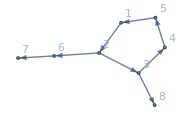

```mathematica
(*Create an undirected cyclic graph*)graph=Graph[{1->2,2->3,3->4,4->5,2->6,6->7,3->8,5->1},VertexLabels->"Name"];

(*Perform a depth-first search starting from node 1 with a maximum depth of 3*)
result=ResourceFunction["DepthFirstSearch"][graph,1,3]

(*Output the result*)
result

(*Highlight the depth-first search path on the graph*)
HighlightGraph[graph,PathGraph[result]]
```

```mathematica
boston = GeoGraphics[GeoBoundsRegion[{{28.0600,28.0900},{-82.4843, -82.4521}}]]
```

```mathematica
atl = GeoBoundsRegion[{{33.7501,33.7901},{-90.3543, -90.3101}}]
Head[atl]
atlanta = GeoGraphics[atl]
```

GeoBoundsRegion[{{33.7501,33.7901},{-90.3543,-90.3101}}]

GeoBoundsRegion

-Graphics-

```mathematica
osmAtlanta=ResourceFunction["OSMImport"][atl]
```

```mathematica
GeoGraphics[Values[Line[Values[osmAtlanta[["Nodes",#Nodes,"Position"]]]]&/@Select[osmAtlanta["Ways"],KeyExistsQ[#Tags,"highway"]&]]]
```

-Graphics-

```mathematica
trafficSignals=Select[osm["Nodes"],MatchQ[#[["Tags","highway"]],"traffic_signals"]&];
positions=Lookup[#,"Position"]&/@trafficSignals
```

```mathematica
GeoGraphics[Point/@positions]
```

-Graphics-

```mathematica
findLengthKPath[k_Integer, st_Integer, g_]:=
Module[{rando := RandomSample[Range[VertexCount[g]]]},
candidatePaths = Table[FindPath[g, st, rando[[i]], {k}], {i, 1, VertexCount[g]}];
Select[candidatePaths, Length[#]>0&, 1]
]
```

```mathematica
findLengthKCycle[k_Integer, st_Integer, g_]:=
Module[{rando := RandomSample[FindCycle[{g, st}, {k}, All]]},
rando[[1]]
]
```

{1,2,3,4,5,6,12,11,10,9,15}

```mathematica
Head[foundPath]
```

List

{16,15,21,22}

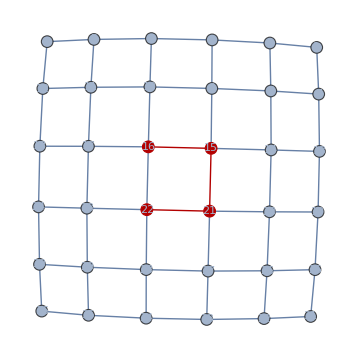

```mathematica
foundPath = Flatten[findLengthKPath[3, 16]]
HighlightGraph[myGraph, PathGraph[foundPath]]
```

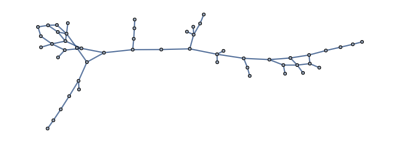

```mathematica
randomG = Graph[{1<->2,2<->3,3<->4, 4<->5, 5<->6, 6<->7, 6<->9, 5<->8, 8<->9, 9<->10, 8<->11, 11<->12, 9<->12, 12<->13, 11<->14, 14<->15, 15<->16, 14<->17, 17<->18, 17<->19, 17<->20, 20<->21, 21<->22, 21<->23, 21<->24, 24<->25, 20<->26, 26<->27, 27<->28, 28<->29, 29<->30, 27<->31, 31<->32, 32<->33, 33<->34, 33<->35, 35<->36, 36<->37, 37<->38, 31<->39, 32<->40, 39<->40, 40<->41, 41<->42, 39<->42, 42<->43, 43<->44, 39<->44, 44<->45, 43<->46, 43<->47, 47<->48, 48<->49, 49<->50, 42<->50, 41<->50, 49<->51, 41<->51, 41<->52}]
```

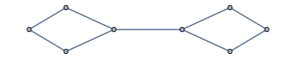

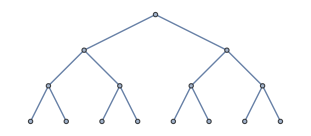

```mathematica
simpleG1 = Graph[{1<->2, 1<->3, 2<->4, 3<->4, 4<->5, 5<->6, 5<->7, 6<->8, 7<->8}]
simpleG2 = Graph[Flatten[Table[{i<->2*i, i<->2*i+1}, {i, 1, 7}]]]
```

```mathematica
Clear[foundPath]
```

{1,2,3,4,5,6,9,8,11,14,17,20,26,27,31,39,42,41,40,32,33,34}

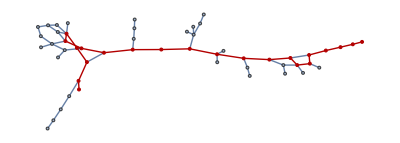

```mathematica
foundPath = Flatten[findLengthKPath[21, 1, randomG]]
HighlightGraph[randomG, PathGraph[foundPath]]
```

```mathematica
FindCycle[{myGraph, 1}, {16}, All]
```

{48<->47,47<->43,43<->44,44<->39,39<->31,31<->32,32<->40,40<->41,41<->51,51<->49,49<->48}

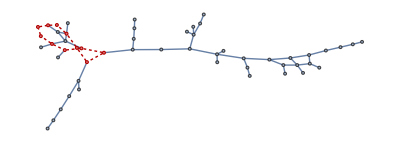

GeoGraphPlot::ngeoedges: {GeoPosition[{500,-300}],GeoPosition[{501,-301}]} is not a list of geo edges

```mathematica
foundCycle = findLengthKCycle[11, 48, randomG]
HighlightGraph[randomG, PathGraph[foundCycle], GraphHighlightStyle->"Dotted"]
```

```mathematica
GeoGraphPlot[{GeoPosition[{50,60.1}]<->GeoPosition[{50.125,59.1}]}, GraphLayout->"Walking"]
```

-Graphics-

```mathematica
GeoGraphPlot[{Entity["Building","TheLouvre::vqy3g"]<->Entity["Building","EiffelTower::5h9w8"]}, GraphLayout->"Walking"]
```

-Graphics-

```mathematica
GeoGraphPlot[{]<->Entity["Building","EiffelTower::5h9w8"]}, GraphLayout->"Walking"]
```

```mathematica
GeoGraphics[Values[Line[Values[osm[["Nodes",#Nodes,"Position"]]]]&/@Select[osm["Ways"],#[["Tags","power"]]==="line"&]]]
```

-Graphics-

```mathematica
toad1 = TravelDirections[{GeoPosition[{50,60.1}], GeoPosition[{50.125,61.1}]}]
```

TravelDirectionsData[…]

```mathematica
toad1["TravelPath"]
```

GeoPath[GeoPosition[…],TravelPath]

```mathematica
nodeSet = {GeoPosition[{28.0667, -82.4826}], GeoPosition[{28.0599, -82.4758}]}
GeoGraphPlot[{nodeSet[[1]]<->nodeSet[[2]]}, GraphLayout->"Walking"]
```

{GeoPosition[{28.0667,-82.4826}],GeoPosition[{28.0599,-82.4758}]}

-Graphics-

#### To-learn theory

- That Stanford fixed-length cycle paper
- ?Short cycles on planar graphs: https://www.mimuw.edu.pl/~kowalik/papers/cycles.pdf
- Euler: https://theory.stanford.edu/~virgi/cs267/papers/cycles-ayz.pdf 
- Cycle Basis??
- Misc: https://hackmd.io/6KM0l_nqRJmNFTH8J3_HCQ